```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[1,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ,m],T=T1[1,m]},
sl1= Module[{J=SR[ω,δ,t,ϵ,m]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,2m}]},ReplacePart[i,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[2m]-c.ConjugateTranspose[T].J.T].c],4]; J=J]; Il1:=Inverse[IdentityMatrix[2m]-sl1.ρ[1,m].SR[ω,δ,t,ϵ,m].ρ[1,m]].sl1;Ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,1,0,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,1,0,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0,m].ρ[1,m].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]]];
η]
```

```mathematica
tr[1,0.0001,1,0,0,7]
```

2.99293

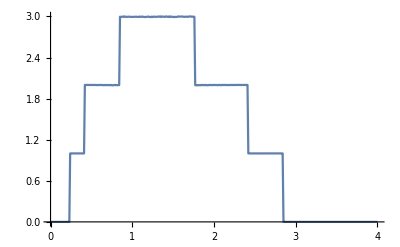

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0,0,7]},{ω,Range[0,4,0.01]}]]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[β[ω,δ,t,ϵ,m]-Module[{κ=β[0,0,0,0,m],i=RandomInteger[{1,14}]},ReplacePart[κ,{{i,i}}->ϵ1]]]
```

```mathematica
imp2[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[β[ω,δ,t,ϵ,m]-Module[{κ=β[0,0,0,0,m],i=RandomInteger[{1,7}],j=RandomInteger[{8,14}]},ReplacePart[κ,{{i,i},{j,j}}->ϵ1]]]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[β[ω,δ,t,ϵ,m]-Module[{κ=β[0,0,0,0,m],i=RandomInteger[{1,7}],j=RandomInteger[{8,14}]},ReplacePart[κ,{{i,i},{j,j}}->0]]]
```

```mathematica
set[ω_,δ_,t_,ϵ_,ϵ1_,m_,x_,y_,z_]:=RandomSample[Join[Table[imp1[ω,δ,t,ϵ,ϵ1,m],x],Table[imp2[ω,δ,t,ϵ,ϵ1,m],y],Table[imp[ω,δ,t,ϵ,0,m],z]]]
```

```mathematica
set[0,0.0001,0,0,0,7,14,0,86]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m],μ=RandomInteger[{1,14}]},ReplacePart[κ,{{μ,μ}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
tr14[ω_,δ_,t_,ϵ_,ϵ1_,m_,numimp_]:=
Module[{x=T1[t,m],T=ρ[t,m]},
list={set[ω,δ,t,ϵ,ϵ1,m,numimp,0,100-numimp]};sl1= Module[{J=SL[ω,δ,t,ϵ,m]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[x].J.x].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,δ,t,ϵ,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ,m].T.sl1.T].SR[ω,δ,t,ϵ,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,ϵ,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]]
```

```mathematica
Mean[Table[tr14[1,0.0001,1,0,0.5,7,14],2000]]
```

2.38756

```mathematica
Mean[Table[tr14[1,0.0001,1,0,0.5,7,14],2000]]
```

2.38729

```mathematica
Export["14imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,14],2000]]},{ω,Range[0,4,0.01]}]]
```

14imp100.csv

```mathematica
Export["28imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,28],2000]]},{ω,Range[0,4,0.01]}]]
```

28imp100.csv

```mathematica
Export["42imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,42],2000]]},{ω,Range[0,4,0.01]}]]
```

42imp100.csv

```mathematica
Export["56imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,56],2000]]},{ω,Range[0,4,0.01]}]]
```

56imp100.csv

```mathematica
Export["70imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,70],2000]]},{ω,Range[0,4,0.01]}]]
```

70imp100.csv

```mathematica
Export["84imp100.csv",Table[{ω,Mean[Table[tr14[ω,0.0001,1,0,0.5,7,84],2000]]},{ω,Range[0,4,0.01]}]]
```

84imp100.csv

```mathematica
Import["84imp100.csv"]
```

{{0.,0.0000256669},{0.01,0.0000189989},{0.02,0.00001612},{0.03,0.0000234811},{0.04,0.000037277},{0.05,0.0000579214},{0.06,0.0000939684},{0.07,0.000126698},{0.08,0.000177977},{0.09,0.000231554},{0.1,0.000323655},{0.11,0.000421093},{0.12,0.000520573},{0.13,0.000668588},{0.14,0.000923648},{0.15,0.00112221},{0.16,0.00147523},{0.17,0.00183169},{0.18,0.0023811},{0.19,0.00332592},{0.2,0.00458534},{0.21,0.00670826},{0.22,0.0107742},{0.23,0.0210489},{0.24,0.0515818},{0.25,0.0671457},{0.26,0.116177},{0.27,0.202495},{0.28,0.280367},{0.29,0.33484},{0.3,0.390629},{0.31,0.39996},{0.32,0.424165},{0.33,0.436759},{0.34,0.460691},{0.35,0.455176},{0.36,0.469866},{0.37,0.462178},{0.38,0.4581},{0.39,0.448695},{0.4,0.446069},{0.41,0.431372},{0.42,0.573382},{0.43,0.614488},{0.44,0.854132},{0.45,0.843172},{0.46,0.672733},{0.47,0.598739},{0.48,0.569418},{0.49,0.546044},{0.5,0.579086},{0.51,0.580975},{0.52,0.584667},{0.53,0.608192},{0.54,0.635657},{0.55,0.650203},{0.56,0.686661},{0.57,0.691764},{0.58,0.724732},{0.59,0.721468},{0.6,0.757405},{0.61,0.792364},{0.62,0.792172},{0.63,0.764135},{0.64,0.825777},{0.65,0.827106},{0.66,0.842147},{0.67,0.845954},{0.68,0.856692},{0.69,0.884533},{0.7,0.870034},{0.71,0.887789},{0.72,0.887107},{0.73,0.898593},{0.74,0.932904},{0.75,0.928441},{0.76,0.917393},{0.77,0.918719},{0.78,0.948699},{0.79,0.950306},{0.8,0.971743},{0.81,0.946266},{0.82,0.939197},{0.83,0.908163},{0.84,0.840435},{0.85,0.73852},{0.86,0.723064},{0.87,0.91648},{0.88,0.862653},{0.89,0.713863},{0.9,0.650416},{0.91,0.618718},{0.92,0.615622},{0.93,0.675074},{0.94,0.710395},{0.95,0.748044},{0.96,0.835626},{0.97,0.867411},{0.98,0.95797},{0.99,1.00249},{1.,1.04862},{1.01,1.1977},{1.02,1.07091},{1.03,0.83396},{1.04,0.482947},{1.05,0.36114},{1.06,0.352868},{1.07,0.357313},{1.08,0.343536},{1.09,0.327796},{1.1,0.331424},{1.11,0.34255},{1.12,0.353471},{1.13,0.365987},{1.14,0.390354},{1.15,0.412715},{1.16,0.440363},{1.17,0.452252},{1.18,0.479135},{1.19,0.479827},{1.2,0.518},{1.21,0.520554},{1.22,0.54664},{1.23,0.562175},{1.24,0.536803},{1.25,0.576381},{1.26,0.595465},{1.27,0.559718},{1.28,0.581001},{1.29,0.561169},{1.3,0.582898},{1.31,0.578431},{1.32,0.591101},{1.33,0.603424},{1.34,0.56331},{1.35,0.597483},{1.36,0.609614},{1.37,0.623132},{1.38,0.616885},{1.39,0.57738},{1.4,0.583798},{1.41,0.586324},{1.42,0.56584},{1.43,0.590961},{1.44,0.578414},{1.45,0.546952},{1.46,0.539727},{1.47,0.556639},{1.48,0.55093},{1.49,0.570444},{1.5,0.550039},{1.51,0.53663},{1.52,0.528229},{1.53,0.515118},{1.54,0.515155},{1.55,0.503403},{1.56,0.469982},{1.57,0.471684},{1.58,0.454953},{1.59,0.441775},{1.6,0.447276},{1.61,0.450772},{1.62,0.441849},{1.63,0.427856},{1.64,0.422307},{1.65,0.413639},{1.66,0.444274},{1.67,0.46836},{1.68,0.482617},{1.69,0.459864},{1.7,0.56797},{1.71,0.561345},{1.72,0.769245},{1.73,0.847755},{1.74,0.988987},{1.75,1.43548},{1.76,1.95669},{1.77,2.18192},{1.78,1.94532},{1.79,1.66382},{1.8,1.29621},{1.81,1.00634},{1.82,0.627342},{1.83,0.432111},{1.84,0.358489},{1.85,0.386108},{1.86,0.4211},{1.87,0.437332},{1.88,0.459347},{1.89,0.489392},{1.9,0.515939},{1.91,0.497008},{1.92,0.527905},{1.93,0.544246},{1.94,0.56256},{1.95,0.555596},{1.96,0.557869},{1.97,0.557474},{1.98,0.539656},{1.99,0.554876},{2.,0.555833},{2.01,0.552623},{2.02,0.552957},{2.03,0.539115},{2.04,0.549156},{2.05,0.522913},{2.06,0.554357},{2.07,0.545467},{2.08,0.52524},{2.09,0.527733},{2.1,0.512278},{2.11,0.505787},{2.12,0.51041},{2.13,0.490764},{2.14,0.488614},{2.15,0.470669},{2.16,0.474351},{2.17,0.484668},{2.18,0.469338},{2.19,0.44773},{2.2,0.427778},{2.21,0.428487},{2.22,0.409069},{2.23,0.399031},{2.24,0.396616},{2.25,0.386847},{2.26,0.370467},{2.27,0.367111},{2.28,0.356724},{2.29,0.337399},{2.3,0.331802},{2.31,0.32037},{2.32,0.323705},{2.33,0.306328},{2.34,0.305959},{2.35,0.302629},{2.36,0.309864},{2.37,0.320854},{2.38,0.364526},{2.39,0.456559},{2.4,0.585437},{2.41,1.08904},{2.42,1.50655},{2.43,1.34966},{2.44,1.07856},{2.45,0.859064},{2.46,0.563153},{2.47,0.345334},{2.48,0.235462},{2.49,0.211205},{2.5,0.210865},{2.51,0.214988},{2.52,0.231733},{2.53,0.237222},{2.54,0.235089},{2.55,0.234385},{2.56,0.249907},{2.57,0.25515},{2.58,0.254012},{2.59,0.259406},{2.6,0.247282},{2.61,0.25523},{2.62,0.249943},{2.63,0.252752},{2.64,0.236868},{2.65,0.243848},{2.66,0.244888},{2.67,0.244658},{2.68,0.235253},{2.69,0.223845},{2.7,0.234603},{2.71,0.219334},{2.72,0.224604},{2.73,0.206961},{2.74,0.202448},{2.75,0.198567},{2.76,0.191708},{2.77,0.177843},{2.78,0.177543},{2.79,0.157319},{2.8,0.151553},{2.81,0.151369},{2.82,0.143331},{2.83,0.145089},{2.84,0.161367},{2.85,0.343179},{2.86,0.315017},{2.87,0.262845},{2.88,0.176192},{2.89,0.102153},{2.9,0.0408976},{2.91,0.00982754},{2.92,0.00567449},{2.93,0.00378254},{2.94,0.00288802},{2.95,0.00215519},{2.96,0.0019008},{2.97,0.00144753},{2.98,0.00111629},{2.99,0.000985938},{3.,0.000792018},{3.01,0.000701487},{3.02,0.000549055},{3.03,0.000557589},{3.04,0.000434561},{3.05,0.000374919},{3.06,0.000344786},{3.07,0.000274201},{3.08,0.000259056},{3.09,0.000252574},{3.1,0.000218123},{3.11,0.000180879},{3.12,0.000178299},{3.13,0.000152505},{3.14,0.000139457},{3.15,0.00013576},{3.16,0.000118458},{3.17,0.000114014},{3.18,0.0000940604},{3.19,0.0000765488},{3.2,0.0000792855},{3.21,0.0000740506},{3.22,0.0000641143},{3.23,0.0000608087},{3.24,0.000054112},{3.25,0.0000514204},{3.26,0.0000482482},{3.27,0.0000433462},{3.28,0.0000389209},{3.29,0.0000368209},{3.3,0.0000338652},{3.31,0.0000306709},{3.32,0.0000313644},{3.33,0.0000292866},{3.34,0.0000251948},{3.35,0.0000240718},{3.36,0.0000216347},{3.37,0.0000228873},{3.38,0.0000208359},{3.39,0.0000193423},{3.4,0.0000186511},{3.41,0.0000168147},{3.42,0.0000156757},{3.43,0.0000140085},{3.44,0.0000127765},{3.45,0.0000116829},{3.46,0.0000127843},{3.47,0.0000122886},{3.48,0.0000115657},{3.49,0.0000107211},{3.5,9.86356×10^-6},{3.51,8.86886×10^-6},{3.52,9.28114×10^-6},{3.53,8.64296×10^-6},{3.54,7.46341×10^-6},{3.55,7.00248×10^-6},{3.56,7.6218×10^-6},{3.57,6.76881×10^-6},{3.58,5.73631×10^-6},{3.59,5.95507×10^-6},{3.6,6.25681×10^-6},{3.61,5.45136×10^-6},{3.62,4.96235×10^-6},{3.63,4.80744×10^-6},{3.64,4.62476×10^-6},{3.65,4.49428×10^-6},{3.66,4.1724×10^-6},{3.67,4.27605×10^-6},{3.68,4.16963×10^-6},{3.69,3.78995×10^-6},{3.7,3.63822×10^-6},{3.71,3.12319×10^-6},{3.72,3.20091×10^-6},{3.73,3.39032×10^-6},{3.74,2.89643×10^-6},{3.75,3.02068×10^-6},{3.76,2.6448×10^-6},{3.77,2.4921×10^-6},{3.78,2.44707×10^-6},{3.79,2.27048×10^-6},{3.8,2.26698×10^-6},{3.81,2.19559×10^-6},{3.82,2.17068×10^-6},{3.83,1.95604×10^-6},{3.84,1.86047×10^-6},{3.85,1.73482×10^-6},{3.86,1.60705×10^-6},{3.87,1.57725×10^-6},{3.88,1.59708×10^-6},{3.89,1.51315×10^-6},{3.9,1.52101×10^-6},{3.91,1.41063×10^-6},{3.92,1.28×10^-6},{3.93,1.28842×10^-6},{3.94,1.24718×10^-6},{3.95,1.19404×10^-6},{3.96,1.14624×10^-6},{3.97,1.10963×10^-6},{3.98,1.04176×10^-6},{3.99,9.59407×10^-7},{4.,9.68192×10^-7}}

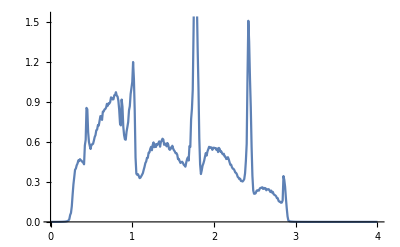

```mathematica
ListPlot[%56,Joined->True]
```

```mathematica
-
```

```mathematica
υ[num_,x_,y_]:=Module[{μ1=RandomInteger[{1,1000}]},
m5=Table[{ω,tr1[ω,0.0001,1,0,0.5,7]},{ω,Range[0,4,0.01]}];ρ2:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/14imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/28imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/42imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/56imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/70imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/84imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/100imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/114imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ10:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/126imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ11:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/140imp100.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ12:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/156imp7.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
*)list:={{2,ρ2},{3,ρ3},{4,ρ4},{5,ρ5},{6,ρ6},{7,ρ7},{8,ρ8},{9,ρ9},{10,ρ10},{11,ρ11}(*,{12,ρ12}*)};Print[{μ1,list}];{list[[Position[list,Min[list]][[1,1]],1]],Min[list],ListLinePlot[m5,PlotStyle->Red]}]
```

```mathematica
υ[0,2,0]
```

Import::nffil: File /home/shardulmukim/14imp100.csv not found during Import.

Part::take: Cannot take positions 1 through 400 in $Failed.

Part::partd: Part specification $Failed⟦1;;400,1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

Import::nffil: File /home/shardulmukim/28imp100.csv not found during Import.

Part::take: Cannot take positions 1 through 400 in $Failed.

Part::partd: Part specification $Failed⟦1;;400,1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

Import::nffil: File /home/shardulmukim/42imp100.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 400 in $Failed.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1;;400,1;;All⟧⟦1;;All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

$Aborted

```mathematica
Clear[υ]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{x=T1[t,m],T=ρ[t,m],imp1:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*δ-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{2,2}}->ω+ⅈ*δ-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{3,3}}->ω+ⅈ*δ-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{4,4}}->ω+ⅈ*δ-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{5,5}}->ω+ⅈ*δ-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{6,6}}->ω+ⅈ*δ-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{7,7}}->ω+ⅈ*δ-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{8,8}}->ω+ⅈ*δ-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{9,9}}->ω+ⅈ*δ-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*δ-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{11,11}}->ω+ⅈ*δ-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{12,12}}->ω+ⅈ*δ-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{13,13}}->ω+ⅈ*δ-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,δ,t,ϵ,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*δ-ϵ1]]]},
list={RandomSample[{imp5,imp14,imp5,imp7,imp14,imp14,imp3,imp3,imp6,imp8,imp9,imp1,imp7,imp6,imp7,imp5,imp3,imp5,imp11,imp10,imp2,imp9,imp8,imp7,imp7,imp8,imp14,imp2,imp3,imp6,imp7,imp12,imp1,imp6,imp7,imp8,imp8,imp13,imp4,imp10,imp14,imp3,imp6,imp3,imp4,imp12,imp3,imp2,imp14,imp8,imp5,imp4,imp13,imp13,imp5,imp1,imp9,imp9,imp1,imp10,imp9,imp6,imp2,imp9,imp2,imp12,imp9,imp14,imp4,imp3,imp6,imp4,imp5,imp12,imp8,imp2,imp4,imp9,imp11,imp8,imp11,imp8,imp4,imp4,imp1,imp12,imp8,imp8,imp1,imp1,imp1,imp13,imp1,imp10,imp5,imp7,imp1,imp3,imp1,imp8}]};η=Module[{},(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,δ,t,ϵ,m]},Do[J=Inverse[IdentityMatrix[14]-list[[1,ζ]].ConjugateTranspose[x].J.x].list[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,δ,t,ϵ,m].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ,m].T.sl1.T].SR[ω,δ,t,ϵ,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,ϵ,m].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>3,3,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];η]
```

```mathematica
Mean[Table[tr1[1,0.0001,1,0,0.5,7],2000]]
```

1.05174

```mathematica
Mean[%72]
```

1.05407

```mathematica
StandardDeviation[%72]
```

0.462078

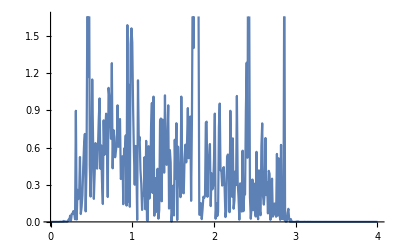

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.0001,1,0,0.5,7]},{ω,Range[0,4,0.01]}]]
```

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.0001,1,0,0.3,7]},{ω,Range[0,4,0.01]}],PlotStyle->RGBColor[0.5,RandomReal[{0,1}],RandomReal[{0,1}]]]
```

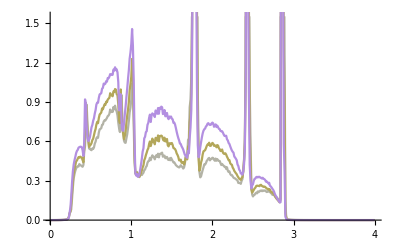

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/100imp100.csv"],PlotStyle->RGBColor[0.7,RandomReal[{0,1}],RandomReal[{0,1}]]],ListLinePlot[Import["/home/shardulmukim/80imp100.csv"],PlotStyle->RGBColor[0.7,RandomReal[{0,1}],RandomReal[{0,1}]]](*,ListLinePlot[Import["/home/shardulmukim/90imp100.csv"],PlotStyle->RGBColor[0.7,RandomReal[{0,1}],RandomReal[{0,1}]]]*),ListLinePlot[Import["/home/shardulmukim/60imp100.csv"],PlotStyle->RGBColor[0.7,RandomReal[{0,1}],RandomReal[{0,1}]]]]
```